```mathematica
(*Patryk Michalak - MetNum Grupa 2 - Zestaw A*)
```

```mathematica
(*zad3*)
Points = {{-2,3},{1,1},{2,-3},{4,8}}
func := Interpolation[Points]
```

```mathematica
func // Table
```

InterpolatingFunction[…]

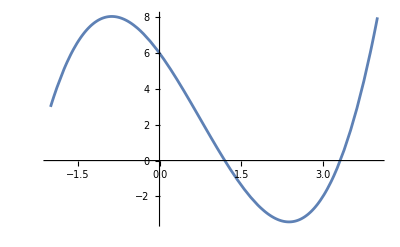

```mathematica
InterpolatingFunction[…]
Plot[%[x],{x,-2,4}]
```

```mathematica
(*zad4*)
P = ({{2, 1, 1}, {1, -4, 3}, {3, 2, 2}})
Psys = ({{7}, {2}, {13}})
{loup,q,w}=LUDecomposition[P]
lo = LowerTriangularize[loup,-1] + IdentityMatrix[3] // MatrixForm
up = UpperTriangularize[loup] // MatrixForm
solo = LinearSolve[lo,Psys] // MatrixForm
LinearSolve[up,solo] // MatrixForm
```

{{2,1,1},{1,-4,3},{3,2,2}}

{{7},{2},{13}}

{{{1,-4,3},{2,9,-5},{3,14/9,7/9}},{2,1,3},0}

(1 | 0 | 0
2 | 1 | 0
3 | 14/9 | 1)

(1 | -4 | 3
0 | 9 | -5
0 | 0 | 7/9)

LinearSolve[(1 | 0 | 0
2 | 1 | 0
3 | 14/9 | 1),{{7},{2},{13}}]

LinearSolve[(1 | -4 | 3
0 | 9 | -5
0 | 0 | 7/9),LinearSolve[(1 | 0 | 0
2 | 1 | 0
3 | 14/9 | 1),{{7},{2},{13}}]]

```mathematica
(*zad5*)
M := ({{1, 2, 3, 3}, {3, 4, 4, 5}, {2, 2, 1, 2}, {4, 6, 7, 8}})
Fre := ({{9}, {16}, {7}, {25}})
LinearSolve[M,Fre]
```

{{-2},{11/2},{0},{0}}

```mathematica
(*zad6*)
f[x_,y_] := x^2 * √y
h = .1
yrk[0] = 1
x[n_]:= n*h
yrk[n_ ] := Module[{k1,k2},
k1=h*f[x[n-1],yrk[n-1]];
k2= h * f[x[n-1]+h,yrk[n-1]+k1];
yrk[n+1] = yrk[n]+1/2 * (k1+k2)]
rktable = Table[yrk[i],{i,0,10}]
```

0.1

1

{1,1.10294,1.21293,1.33209,1.46264,1.60685,1.76704,1.94557,2.14486,2.36732,2.61541}